# Exercise 2.2

## Task a)

```mathematica
(*Task a)*)
ClearAll["Global`*"]
A={{σ+1,3},{-2,σ-1}};
Eigenvalues[A]
```

{-ⅈ √5+σ,ⅈ √5+σ}

## Task b)

```mathematica
(*Task b)*)
ClearAll["Global`*"]
A={{σ+1,3},{-2,σ-1}};

x0={u,v}; 

x[t_]={x1[t],x2[t]};

solution[t_,u_,v_]=DSolve[{x'[t]==A.x[t],x[0]==x0},x[t],t];

xSolution[t_,u_,v_]=x[t]/. solution[t,u,v][[1]];

{x1Solution[t_,u_,v_],x2Solution[t_,u_,v_]}=Simplify[xSolution[t,u,v]]
```

{1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 (u+3 v) Sin[√5 t]),1/5 ⅇ^(t σ) (5 v Cos[√5 t]-√5 (2 u+v) Sin[√5 t])}

## Task c)

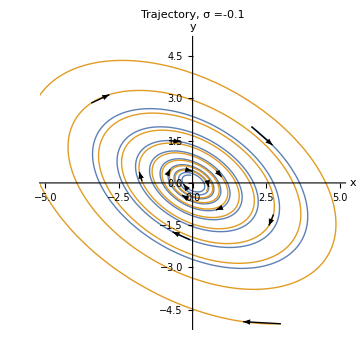

```mathematica
(*Task c)*)
Clear[σ,u,v,values]
σ = -0.1;

(*u and v changes starting position and amplitude of oscillations.*)

xSol[t_,u_,v_]=xSolution[t,u,v][[1]];
ySol[t_,u_,v_]=xSolution[t,u,v][[2]];

(*Initial conditions*)
values={{2,2},{3,-5}};

plots=Table[Module[{u,v},{u,v}=values[[i]];
ParametricPlot[Evaluate[{xSol[t,u,v],ySol[t,u,v]}],{t,0,25},
PlotStyle->Directive[ColorData[97,i],Thick],
PlotRange->{{-5,5},{-5,5}},
AxesLabel->{"x","y"},
PlotLabel->"Trajectory, σ ="<> ToString[σ]]],
{i,1,Length[values]}];

arrows=Graphics[Table[Module[{u,v},{u,v}=values[[i]];
Table[Arrow[{Evaluate[{xSol[t,u,v],ySol[t,u,v]}],
Evaluate[{xSol[t+0.1,u,v],ySol[t+0.1,u,v]}] }],
{t,0,24,4}]],{i,1,Length[values]}]];

Show[plots,arrows,ImageSize->Medium]
```

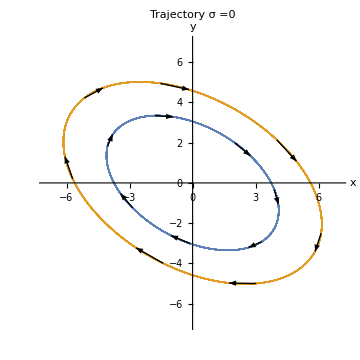

```mathematica
Clear[σ,u,v]
σ = 0;

xSol[t_,u_,v_]=xSolution[t,u,v][[1]];
ySol[t_,u_,v_]=xSolution[t,u,v][[2]];

(*Initial conditions*)
values={{2,2},{3,-5}};

plots=Table[Module[{u,v},{u,v}=values[[i]];
ParametricPlot[Evaluate[{xSol[t,u,v],ySol[t,u,v]}],{t,0,25},
PlotStyle->Directive[ColorData[97,i],Thick],
PlotRange->{{-7,7},{-7,7}},
AxesLabel->{"x","y"},
PlotLabel-> "Trajectory σ ="<> ToString[σ]]],
{i,1,Length[values]}];

arrows=Graphics[Table[Module[{u,v},{u,v}=values[[i]];
Table[Arrow[{Evaluate[{xSol[t,u,v],ySol[t,u,v]}],
Evaluate[{xSol[t+0.1,u,v],ySol[t+0.1,u,v]}] }],
{t,0,24,4}]],{i,1,Length[values]}]];

Show[plots,arrows,ImageSize->Medium]
```

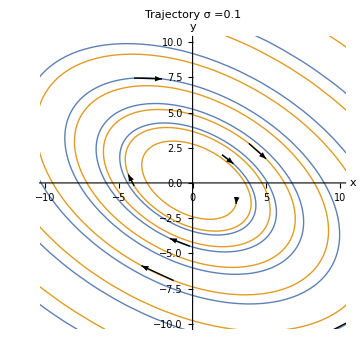

```mathematica
Clear[σ,u,v]
σ = 0.1;
xSol[t_,u_,v_]=xSolution[t,u,v][[1]];
ySol[t_,u_,v_]=xSolution[t,u,v][[2]];

(*Initial conditions*)
values={{2,2},{3,-1}};

plots=Table[Module[{u,v},{u,v}=values[[i]];
ParametricPlot[Evaluate[{xSol[t,u,v],ySol[t,u,v]}],{t,0,25},
PlotStyle->Directive[ColorData[97,i],Thick],
PlotRange->{{-10,10},{-10,10}},
AxesLabel->{"x","y"},
PlotLabel->"Trajectory  σ ="<> ToString[σ]]],
{i,1,Length[values]}];

arrows=Graphics[Table[Module[{u,v},{u,v}=values[[i]];
Table[Arrow[{Evaluate[{xSol[t,u,v],ySol[t,u,v]}],
Evaluate[{xSol[t+0.1,u,v],ySol[t+0.1,u,v]}] }],
{t,0,24,4}]],{i,1,Length[values]}]];

Show[plots,arrows,ImageSize->Medium]
```

## Task d)

```mathematica
(*Task d)*)

(*Angular frequency from studying the answers [x(t),y(t)]]*)
ω=Sqrt[5];

periodTime=2*π/ω
```

(2 π)/(√5)

## Task e)

```mathematica
(*Task e)*)
(*Choose initial conditions (u,v) to (1,1)*)
(*Have tried for multiple initial conditions and they all give the same ratio which is reasonable.*)
u=1;
v = 1;
σ = 0;

(*Copied from task b), use initial conditions u=v=1*)
x [t_,u_,v_]:= 1/5 ⅇ^(t σ) (5 u Cos[√5 t]+√5 (u+3 v) Sin[√5 t])
y[t_,u_,v_] := 1/5 ⅇ^(t σ) (5 v Cos[√5 t]-√5 (2 u+v) Sin[√5 t])

(*The distance of any point on the ellipse from the origin*)
l[t_]:=Sqrt[x[t,u,v]^2+y[t,u,v]^2] //FullSimplify

major=Maximize[l[t],t]//FullSimplify;
minor= Minimize[l[t],t]//FullSimplify;
ratio = major[[1]]/minor[[1]] // FullSimplify
```

1/2 (1+√5)

## Task f)

```mathematica
(*Initial conditions:*)
u= 1;
v = 1;

(*Insert the time at which we reach the major*)
majorVec={x[t,u,v]/. major⟦2,1⟧,y[t,u,v]/. major⟦2,1⟧}//FullSimplify ;

normalization=Norm[majorVec]//FullSimplify;

normalizedVec=majorVec/normalization //Simplify
```

{√(1/10 (5+√5)),-√(2/(5+√5))}